## 1. 问卷数据导入与品质分析

问卷通过”问卷星”在线问卷托管平台进行设计, 发布以及答卷管理. 在2024-10-15 0时许开始对外接收, 至2024-10-21 24时停止收集. 
受访者通过网页查看问卷内容并提交答案.

### 1.1. 问卷Excel导入为Mathematica的嵌套List函数式

```mathematica
ansRaw=Import[NotebookDirectory[]<>"285334255_00001-00078.xlsx","XLSX"]//First;
```

```mathematica
ansRaw//Dimensions
```

{79,105}

Excel每列字段名称提取

```mathematica
ansFields=ansRaw[[1,All]];
MapIndexed[{#2[[1]],#1}&,ansFields]//Grid[#,Alignment->Left]&//Pane[#,{800,300},Scrollbars->{False,True}]&//CreateDialog;
```

### 1.2. 答题时长分析

```mathematica
ansDuration=StringReplace[#,"秒"->""]&/@ansRaw[[2;;,3]];
ansDuration=ToExpression/@ansDuration;
```

### 1.2.1. 基本统计量

```mathematica
Table[stat[ansDuration],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{422.808,962.359,8.33195,72.2406}

结果严重正偏, √M_2, M_3, M_4统计结果受极端值影响严重.

需要检测答题时长的离群值, 在将其移除后重新进行统计.

#### 1.2.2. 异常值检测与移除

10月27日的异常值阈限计算方法有误, 有关算法已经全部更正. (2024-10-28)
错误的异常值检测算法, 导致对异常问卷的判定结论出现错误. 
采用更正后的算法重新计算, 发现原有的判定方法(基于PCA)不可靠, 现已弃用.

依据: {x|Q_1-1.5·IQR≤x≤Q_3+1.5·IQR}范围外的值为异常值, {x|Q_1-3·IQR≤x≤Q_3+3·IQR}范围外的值为严重异常值, 其中IQR=Q_3-Q_1

```mathematica
outlierRemoval//Clear;
outlierRemoval[data_]:=Block[{Q1,Q3,IQR,outlPrtn},
	{Q1,Q3}=data//Quantile[#,{1/4,3/4}]&;
	IQR=Q3-Q1;
	outlPrtn=Reap[Do[
	Which[
		Q1-1.5IQR≤x≤Q3+1.5IQR,Sow[x,"Regular"];,
		Q1-3IQR≤x<Q1-1.5IQR,Sow[x,"LowerOutlier"];,
		Q3+1.5IQR<x≤Q3+3IQR,Sow[x,"UpperOutlier"];,
		x<Q1-3IQR,Sow[x,"LowerFarOutlier"];,
		x>Q3+3IQR,Sow[x,"UpperFarOutlier"]
	],{x,data}]
,{"LowerFarOutlier","LowerOutlier","Regular","UpperOutlier","UpperFarOutlier"}][[2]];
	Return[If[#=!={},First[#],#]&/@outlPrtn];
];
```

```mathematica
ansDuraOutlPrtn=ansDuration//outlierRemoval;
```

```mathematica
ansDuraOU=ansDuraOutlPrtn[[4;;]]//Flatten
```

{759,762,752,8707}

```mathematica
ansDuraFOU=ansDuraOutlPrtn[[5]]
```

{8707}

```mathematica
ansDuraOL=ansDuraOutlPrtn[[;;2]]//Flatten
```

{}

异常高值4个, 均大于600s(10 min), 其中最大值为8707s(折合约2 hr 25 min), 超出Med±3·QI范围; 其余异常值均介于600s(10 min)至900s(15 min)之间, 在Med±3·QI范围以内. 
可能原因推测: 受访者在网络答题过程中因为工作事务中断答题, 下工后提交问卷. 
异常低值0个. 
据此, 无法通过单纯分析异常低值(答题速度异常偏快)判定答卷作答是否出现胡乱填写的情况, 需结合特定问题的答题特征判定.

移除异常值后重新统计

```mathematica
ansDurationRmOtl=ansDuraOutlPrtn[[3]];
```

```mathematica
Table[stat[ansDurationRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{297.284,127.256,0.545704,2.69203}

```mathematica
ansDurationRmFarOtl=ansDuraOutlPrtn[[2;;4]]//Flatten;
```

```mathematica
Table[stat[ansDurationRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{315.221,153.61,1.01363,3.88611}

```mathematica
PairedHistogram[ansDurationRmOtl,ansDurationRmFarOtl,{0,900,30},AxesOrigin->{0,0},Ticks->{Range[0,10,5],Range[0,900,150]}]
```

-Graphics-

筛除异常值和严重异常值的结果, 分别显示作答时长分布呈正偏特征. 进一步分析: 部分受访者作答时长(介于600s至900s)可能非异常值. 
可能原因推测: 1. 问卷题目设置较多, 题目被排版至多个页面, 拖慢部分受访者答题进度. 
2. 问卷中排序题, 量表题比例较大, 由于问卷在线上填写, 大量受访者在答题后期出现疲劳, 加快答题速度.

### 1.3. 排序题质量检测方法

#### 1.3.1. 排序题排序指数

由于问卷题量和排序题比例较大, 受访者可能在尽快完成作答的动机下, 顺次点选排序题中的若干选项. 
问卷发布早期, 部分排序题未设置”选项乱序显示”功能, 前期接收的部分问卷, 对应排序题中的答案可能出现正序排列的现象. 
问卷发布后, 在2024-10-15 15:30(北京时间)许, 对14, 15题启用”选项乱序显示”, 其他排序题的选项显示模式未作变动, 启用前, 已收集31份答卷. 
据此: 可引入一种基于”排序不等式”的指数, 分析用户在排序题中的行为.

```mathematica
seqIndex//Clear;
seqIndex[seq_]:=Block[{nOptn,nOptnSel,seqAsc,seqRnd,seqDesc,phase,sumSortOrd,sumInvOrd,sumRndOrd,seqIdx},
	nOptn=Length[seq];
	seqRnd=Cases[seq,Except[""]];nOptnSel=Length[seqRnd];
	seqDesc=Sort[seqRnd,Greater];seqAsc=Reverse[seqDesc];
	phase=Range[nOptnSel];
	sumSortOrd=seqAsc.phase;sumInvOrd=seqDesc.phase;sumRndOrd=seqRnd.phase;
	If[sumSortOrd==sumInvOrd,Return[0];];
	seqIdx=(sumRndOrd-sumInvOrd)/(sumSortOrd-sumInvOrd);
	seqIdx=(2*seqIdx-1)*nOptnSel/nOptn;
	Return[seqIdx];
]
```

问卷的9, 10, 14, 15题均为排序题, 计算每位受访者在4道排序题的排序指数

```mathematica
ans09SeqIdx=seqIndex/@ansRaw[[2;;,45;;53]];
ans10SeqIdx=seqIndex/@ansRaw[[2;;,54;;59]];
ans14SeqIdx=seqIndex/@ansRaw[[2;;,72;;78]];
ans15SeqIdx=seqIndex/@ansRaw[[2;;,79;;85]];
```

```mathematica
ansSeqIdx={ans09SeqIdx,ans10SeqIdx,ans14SeqIdx,ans15SeqIdx}//Transpose;
```

#### 1.3.2. 排序题排序指数统计分析

对全体问卷, 计算不同排序题排序指数之间的相关系数.

```mathematica
ansSeqIdx//Correlation//MatrixForm
```

(1. | 0.0916738 | 0.195416 | 0.226391
0.0916738 | 1. | -0.169535 | 0.0910686
0.195416 | -0.169535 | 1. | 0.464177
0.226391 | 0.0910686 | 0.464177 | 1.)

对第1~31份问卷, 和第32~78份问卷的排序指数, 分别统计相关系数. 
依据: 前31份问卷的四道排序题均未启用”选项乱序显示”功能; 自第32份问卷起, 对第14, 15题启用”选项乱序显示”, 第9, 10题不启用.

```mathematica
ansSeqIdx[[;;31]]//Correlation//MatrixForm
```

(1. | 0.184699 | 0.384031 | 0.405116
0.184699 | 1. | -0.39325 | -0.0639138
0.384031 | -0.39325 | 1. | 0.54261
0.405116 | -0.0639138 | 0.54261 | 1.)

```mathematica
ansSeqIdx[[32;;]]//Correlation//MatrixForm
```

(1. | 0.00953888 | 0.0389687 | 0.0793816
0.00953888 | 1. | 0.0452229 | 0.251911
0.0389687 | 0.0452229 | 1. | 0.392341
0.0793816 | 0.251911 | 0.392341 | 1.)

第14, 15题间的排序指数相关关系较其他排序题间的关系更为显著, 且为正相关关系. 
可能原因推测: 两题均涉及游客对东湖绿道内导览设施的使用调查. 两道排序题连续出现; 调查内容相似, 但问题面向的情景不同; 选项种类和数量相同; 上述因素共同作用, 导致受访者答题时出现疲劳, 通过顺次选择选项的手段加快答题速度.

此外: 第1~31份问卷中, 第9题与第14, 15题间的排序指数分别呈正相关关系; 第32~78份问卷中, 第9题与第14, 15题间的排序指数没有显著的相关关系. 
可能原因推测: 第9题选项较多, 且第9题未启用"选项乱序显示"; 第14, 15题自第32份问卷起启用"选项乱序显示"

计算各排序题排序指数与作答时长的相关系数:

```mathematica
MapThread[Flatten[{##1}]&,{ansSeqIdx,ansDuration}]//Correlation//Last//Most//MatrixForm
```

(-0.305022
0.196317
-0.243674
-0.13301)

#### 1.3.3. 排序题异常结果提取

对每份问卷, 当排序题9, 10, 14中的任一道的排序指数被识别为异常值时, 则将问卷视为异常问卷

```mathematica
ans09SeqIdxOutlPrtn=ans09SeqIdx//outlierRemoval;
ans14SeqIdxOutlPrtn=ans14SeqIdx//outlierRemoval;
ans15SeqIdxOutlPrtn=ans15SeqIdx//outlierRemoval;
```

```mathematica
ans09OutlierIdx=Map[Position[ans09SeqIdx,#]&,ans09SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
ans14OutlierIdx=Map[Position[ans14SeqIdx,#]&,ans14SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
ans15OutlierIdx=Map[Position[ans15SeqIdx,#]&,ans15SeqIdxOutlPrtn//Drop[#,{3}]&//Flatten]//Flatten;
```

```mathematica
ansOutlierIdx=List/@Union[ans09OutlierIdx,ans14OutlierIdx,ans15OutlierIdx]
```

{{2},{5},{15},{20},{21},{44},{67},{69},{78}}

#### 1.3.4. 排序题异常结果筛除比对

统计排序题

```mathematica
rankingMatrix//Clear;
rankingMatrix[ans_]:=Block[{nOptn,ord,matOrd},
	nOptn=ans[[1]]//Length;
	ord=ans//Transpose;
	matOrd=Table[Count[ord[[idxItem]],idxOrd//N],{idxItem,nOptn},{idxOrd,nOptn}];
	Return[matOrd];
];
```

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,45;;53]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{42 | 7 | 0 | 1 | 1 | 2 | 0 | 0 | 1
5 | 13 | 2 | 1 | 2 | 2 | 3 | 1 | 1
0 | 13 | 11 | 3 | 4 | 1 | 0 | 0 | 0
7 | 2 | 3 | 10 | 4 | 3 | 2 | 1 | 0
8 | 5 | 9 | 5 | 7 | 3 | 1 | 2 | 0
1 | 8 | 7 | 0 | 0 | 6 | 1 | 5 | 3
6 | 2 | 6 | 3 | 2 | 2 | 7 | 2 | 3
7 | 7 | 5 | 2 | 4 | 0 | 3 | 5 | 2
2 | 1 | 1 | 6 | 1 | 3 | 1 | 2 | 6,34 | 7 | 0 | 1 | 1 | 1 | 0 | 0 | 1
5 | 7 | 2 | 1 | 2 | 2 | 1 | 1 | 1
0 | 12 | 5 | 3 | 3 | 0 | 0 | 0 | 0
7 | 2 | 3 | 3 | 2 | 3 | 2 | 1 | 0
8 | 4 | 9 | 3 | 2 | 3 | 1 | 1 | 0
1 | 8 | 4 | 0 | 0 | 0 | 1 | 5 | 3
6 | 2 | 6 | 3 | 2 | 2 | 2 | 1 | 1
6 | 6 | 5 | 2 | 3 | 0 | 2 | 0 | 2
2 | 1 | 1 | 6 | 1 | 2 | 1 | 1 | 1}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,54;;58]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{19 | 6 | 4 | 3 | 2
27 | 17 | 8 | 2 | 0
11 | 7 | 5 | 3 | 4
7 | 6 | 1 | 4 | 4
14 | 8 | 2 | 2 | 3,16 | 5 | 2 | 2 | 2
23 | 14 | 6 | 2 | 0
10 | 5 | 4 | 1 | 4
7 | 6 | 1 | 3 | 1
13 | 7 | 1 | 2 | 2}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,72;;78]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{35 | 9 | 4 | 4 | 3 | 1 | 0
6 | 13 | 10 | 8 | 1 | 1 | 0
3 | 10 | 8 | 7 | 9 | 2 | 0
25 | 17 | 10 | 3 | 2 | 1 | 0
7 | 5 | 7 | 6 | 4 | 4 | 0
2 | 5 | 6 | 3 | 3 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3,29 | 9 | 3 | 3 | 2 | 1 | 0
5 | 10 | 9 | 8 | 0 | 0 | 0
3 | 8 | 7 | 5 | 8 | 1 | 0
24 | 16 | 10 | 1 | 1 | 0 | 0
6 | 4 | 4 | 6 | 3 | 3 | 0
2 | 3 | 4 | 2 | 2 | 7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,79;;85]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{30 | 14 | 5 | 6 | 2 | 1 | 0
9 | 20 | 5 | 4 | 3 | 1 | 0
7 | 4 | 9 | 2 | 3 | 5 | 0
10 | 11 | 10 | 9 | 2 | 0 | 0
11 | 3 | 6 | 5 | 6 | 2 | 0
11 | 6 | 7 | 3 | 3 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6,26 | 11 | 5 | 4 | 2 | 1 | 0
8 | 16 | 5 | 4 | 1 | 1 | 0
6 | 4 | 5 | 1 | 3 | 4 | 0
9 | 10 | 9 | 5 | 1 | 0 | 0
9 | 2 | 4 | 5 | 3 | 2 | 0
11 | 6 | 6 | 3 | 3 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4}

对比筛除前后各排序题的排序统计结果, 异常问卷在一定程度上影响了排序题调研结果的准确性. 
据此, 后续问卷分析中, 对排序题的统计分析, 以及排序题结果与其他题型结果的交叉统计分析工作, 需要排除异常问卷; 对其他题型的统计分析工作, 仍采用全体问卷.

## 2. 受访者基本信息分析

### 2.1. 性别, 年龄和职位分析

#### 2.1.1. 性别比例

```mathematica
ansGender=ansRaw[[2;;,8]];
```

```mathematica
Tally[ansGender]
```

{{1.,58},{2.,20}}

男性受访者数量远高于女性, 男女比例接近3:1

#### 2.1.2. 年龄分布

```mathematica
ansAge=ansRaw[[2;;,9]];
```

```mathematica
Table[stat[ansAge],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{29.4231,11.7003,3.23922,18.3889}

结果严重正偏, M_4统计结果受极端值影响严重.

需要检测年龄的离群值, 在将其移除后重新进行统计.

```mathematica
ansAgeOutlPrtn=ansAge//outlierRemoval;
```

```mathematica
ansAgeOU=ansAgeOutlPrtn[[4;;]]//Flatten
```

{51.,50.,51.,51.,51.,47.,100.}

```mathematica
ansAgeFOU=ansAgeOU=ansAgeOutlPrtn[[5]]
```

{100.}

```mathematica
ansAgeOL=ansAgeOutlPrtn[[;;2]]//Flatten
```

{}

异常高值7个, 均大于40a, 其中最大值为100a, 超出Med±3·QI范围, 其余异常值均介于40a至60a之间, 在Med±3·QI范围以内. 
可能原因推测: 年龄题采用拖拽滑块的方式填写, 滑块两端对应的年龄分别为0a和100a, 填写年龄为100a的用户误将滑块拖动至末尾
异常低值0个.

移除异常值后重新统计

```mathematica
ansAgeRmOtl=ansAgeOutlPrtn[[3]];
```

```mathematica
Table[stat[ansAgeRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{26.6761,5.89134,0.883226,3.20363}

```mathematica
ansAgeRmFarOtl=ansAgeOutlPrtn[[2;;4]]//Flatten;
```

```mathematica
Table[stat[ansAgeRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{28.5065,8.50329,1.30437,4.02478}

```mathematica
PairedHistogram[ansAgeRmOtl,ansAgeRmFarOtl,{0,60,2},AxesOrigin->{10,0},Ticks->{Range[0,25,5],Range[0,60,10]}]
```

-Graphics-

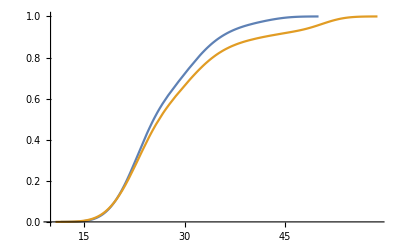

```mathematica
{ansAgeRmOtl,ansAgeRmFarOtl}//SmoothHistogram[#,Automatic,"CDF",AxesOrigin->{10,0}]&
```

分别筛除异常值和严重异常值的结果, 分别显示年龄分布呈正偏特征. 进一步分析: 部分受访者填写的年龄数据(介于40a至60a)可能非异常值. 
可能原因推测: 多数(近80%)受访者年龄在20~40岁之间, 少数(近10%)位于40~60岁之间, 考虑到问卷通过网络发布和填写, 这一分布特征与移动互联网用户的年龄特征吻合程度较好.